```mathematica
Expand[(x+1)^10]
```

1+10 x+45 x^2+120 x^3+210 x^4+252 x^5+210 x^6+120 x^7+45 x^8+10 x^9+x^10

```mathematica
(* 拼写错误的例子 *)
Expandd[(x+2)^2]
```

Expandd[(2+x)^2]

```mathematica
(* 拼写错误的例子 *)
Table[]
```

Table::argm: 调用 Table 时使用了 0 个参数；应该用 1 个或更多参数.

Table[]

```mathematica
Range[1,12,3]
```

{1,4,7,10}

```mathematica
(* 错误使用Range函数的例子 *)
Range[1,12,1,1]
```

Range::argb: 调用 Range 时使用了 4 个参数；应该用 1 到 3 个参数.

Range[1,12,1,1]

```mathematica
(* 未匹配的括号 *)
Expand[(X+2)^6
```

```mathematica
2*3+4*5
```

26

```mathematica
2(3+4)5
```

70

```mathematica
(* 查看Wolfram如何解释一个表达式 *)
FullForm[a b+c d]
```

Plus[Times[a,b],Times[c,d]]

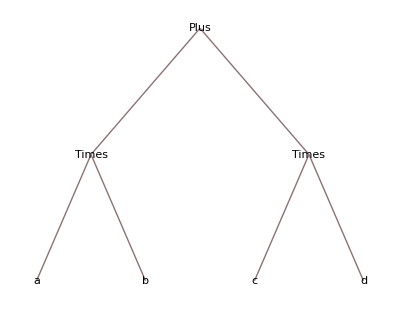

```mathematica
TreeForm[a b + c d]
```

```mathematica
TraditionalForm[a b + c d]
```

a b+c d

```mathematica
(* 大型计算 *)
2^(10+20-15) + 3^(10+20-15) + 4^(10 + 20 - 15)
```

1088123499

```mathematica
(* 定义变量 *)
x = 10;
```

```mathematica
2^x
```

1024

```mathematica
x == 5
```

False

```mathematica
a = (10 + 20 - 15);
```

```mathematica
2^a+3^a + 4^a
```

1088123499

```mathematica
a = 12;
```

```mathematica
2^a+3^a + 4^a
```

17312753

```mathematica
(* 清除变量的定义 *)
Clear[a]
```

```mathematica
(* 创建复合表达式 *)
a = 10+ 20 - 18;
2^a + 3^a + 4^a
```

17312753

```mathematica
a = 10+ 20 - 18;2^a + 3^a + 4^a
```

17312753

```mathematica
{1^2, 2^2, 3^2, 4^2, 5^2, 6^2, 7^2, 8^2, 9^2, 10^2 }
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[i^2,{i,0,10}]
```

{0,1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[i^2,{i,0,10, 2}]
```

{0,4,16,36,64,100}

```mathematica
Table[i^2,{i,0,10, 1}]
```

{0,1,4,9,16,25,36,49,64,81,100}

```mathematica
(* 默认情况下i从1开始，若为单参数则是从1一直迭代到该参数指示的值 *)
Table[i^2,{i,10}]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
Table[π,10]
```

{π,π,π,π,π,π,π,π,π,π}

```mathematica
Table[{i,i^2},{i,1,10}]
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

```mathematica
π squared is N[π^2]
```

31.0063 is squared

```mathematica
N[π^3]
```

31.0063

```mathematica
(* 字符串的连接 *)
StringJoin["The first part", " and the second part."]
```

The first part and the second part.

```mathematica
ToString[N[π^2]]
```

9.8696

```mathematica
FullForm[%] (* 上一次的输出为什么类型 *)
```

"9.8696"

```mathematica
StringJoin["π squared is ", ToString[N[π^2]]]
```

π squared is 9.8696

```mathematica
"π squared is "<> ToString[N[π^2]]
```

π squared is 9.8696

```mathematica
(10 m)/s 5s
```

50 m

```mathematica
+
```

1504/127 ft

```mathematica
Quantity[2, "Feet"]
```

2 ft

```mathematica
Quantity[2, "Feet"] + Quantity[3, "Meters"]
```

1504/127 ft

```mathematica
UnitConvert[%,"Meters"]
```

2256/625 m

```mathematica
Quantity[7,"Days"] + Quantity[4,"Weeks"]
```

35 days

```mathematica
(* 打印日期 *)
Today
```

Tue 7 Feb 2023

```mathematica
DateList[DateObject[{2023, 2 , 7}]]
```

{2023,2,7,0,0,0.}

```mathematica
DatePlus[Today, 5]
```

Sun 12 Feb 2023

```mathematica
DatePlus[Today,Quantity[100, "Days"]]
```

Thu 18 May 2023

```mathematica
DatePlus[Today,Quantity[4, "Weeks"]]
```

Tue 7 Mar 2023

```mathematica
DayName[DatePlus[Today,Quantity[5,"Months"]]]
```

Friday

```mathematica
(* 定义函数 *)
f[x_] := x^2
```

```mathematica
f[2]
```

4

```mathematica
f[π]
```

π^2

```mathematica
f[1.23456]
```

1.52414

```mathematica
f[{1,2,3}]
```

{1,4,9}

```mathematica
h[a_, b_] := a^b;
```

```mathematica
h[2,3]
```

8

```mathematica
Clear[x,a,f,h]
```